#### Hook vs area

```mathematica
l0 = 1/Sqrt[3];
sol =NSolve[6 (l-l0)==4/(3 Sqrt[3]l^3),l,Reals]
a = Sqrt[3] sol[[1,1,2]]
A =Sqrt[3] a^2/2
```

{{l→0.814655},{l→-0.493053}}

1.41102

1.72425

#### Tension vs area

```mathematica
sol =NSolve[6==4/(3 Sqrt[3]l^3),l,Reals]
a = Sqrt[3] sol[[1,1,2]]
```

{{l→0.504362}}

0.87358

#### Perimeter Hook vs area

```mathematica
sol = NSolve[6 (6 l-6 l0)==4/(3 Sqrt[3]l^3),l,Reals]
a = Sqrt[3] sol[[1,1,2]]
```

{{l→0.653848},{l→-0.29094}}

1.1325

#### Perimeter Tension vs area

```mathematica
is the same as bond tension like this
```

#### Balance eqn from paper

```mathematica
Clear[R]
param = {L->1,α->-0.5};
T[R_]:=(1+ α)/L^(1+α)R^α;
eqn[A_,p_]:=(-2 A)/R^3+ (1+ α)/L^(1+α)R^α+2 p R == 0
Rsol[A_,p_]:=Select[NSolve[eqn[A,p]/.param,R,Reals][[All,1,2]],#>0 &]
Rdb1[A_,p_]:=(A/p)^(1/4)/.param
Rdb2[A_,p_]:=(2 A L^(1+α)/(1+α))^(1/(3+α))/.param
```

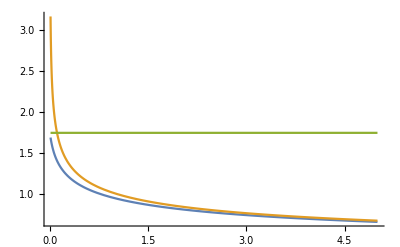

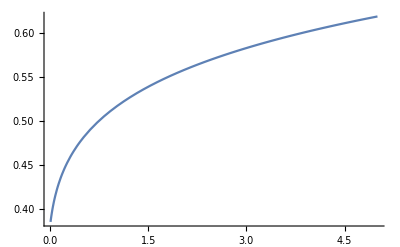

```mathematica
A0 = 1;
Plot[{Rsol[A0,p],Rdb1[A0,p],Rdb2[A0,p]},{p,0.01,5}]
Plot[T[Rsol[A0,p]]/.param,{p,0.01,5}]
```

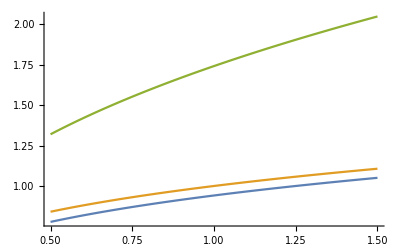

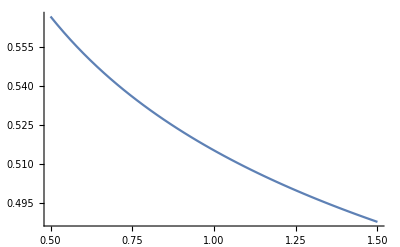

```mathematica
p0 = 1;
Plot[{Rsol[A,p0],Rdb1[A,p0],Rdb2[A,p0]},{A,0.5,1.5}]
Plot[T[Rsol[A,p0]]/.param,{A,0.5,1.5}]
```

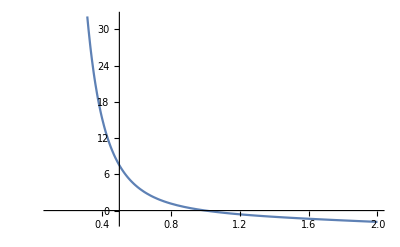

```mathematica
Plot[{1/R^3-R},{R,0.1,2}]
```

```mathematica
H[T_,R0_,R_] := T (R0^3/(2 R^2)+R) +p R^2
D[H[T,R0,R],R]
Solve[D[H[T,R0,R],R]==0/.p->0,R]
```

2 p R+(1-R0^3/R^3) T

{{R→R0},{R→-(-1)^(1/3) R0},{R→(-1)^(2/3) R0}}

```mathematica
Simplify[Series[H[T,R0,R0+u],{u,0,2}]]
```

(p R0^2+(3 R0 T)/2)+2 p R0 u+(p+(3 T)/(2 R0)) u^2+O[u]^3

```mathematica
Simplify[Normal[Series[H[T + t dT,R0+t r,R0+t u]-H[T,R0+r,R0+r]/.p->0,{t,0,2}]]/.t->1]
```

(3 (dT R0 (r+R0)+T (r-u)^2))/(2 R0)

```mathematica
Simplify[Normal[Series[H[T + t dT,R0+t r,R0+t u]/.p->0,{t,0,2}]]/.t->1]
```

(3 (dT R0 (r+R0)+T (r^2+R0^2+r (R0-2 u)+u^2)))/(2 R0)

```mathematica
Simplify[Normal[Series[H[T,R0+t r,R0+t u]-H[T,R0+r,R0+r],{t,0,2}]]/.t->1]
```

-((r-u) (3 T (-r+u)+2 p R0 (r+2 R0+u)))/(2 R0)

```mathematica
Simplify[-((r-u) (r (-3+2 p R0)+3 u+2 p R0 (2 R0+u)))/(2 R0)-(3 (r-u)^2)/(2 R0)]
```

-p (r-u) (r+2 R0+u)